# xSM - Without Z_2

## Now with Tadpoles!!!

## Lagrangian Analytical Relations

## Define the Fields

```mathematica
(*Gauge Fields*)
sigpauli1={{0,1},{1,0}};
sigpauli2={{0,-ⅈ},{ⅈ,0}};
sigpauli3={{1,0},{0,-1}};
eins={{1,0},{0,1}};
(*Gauge Fields*)
gaugefields={Subscript[W, 1],Subscript[W, 2],Subscript[W, 3],B};
cw=g/Sqrt[g^2+Subscript[g, w]^2];
sw=Subscript[g, w]/Sqrt[g^2+Subscript[g, w]^2];
Rot={{cw,-sw},{sw,cw}};
(*Quark weyl spinors*)
QLbar={Subscript[t̄, L],Subscript[b̄, L]};
QL={Subscript[t, L],Subscript[b, L]};
barfermfields={Subscript[t̄, L],Subscript[t̄, R],Subscript[b̄, L],Subscript[b̄, R]};
fermfields={Subscript[t, L],Subscript[t, R],Subscript[b, L],Subscript[b, R]};
Conjugate[Subscript[y, t]]^=Subscript[y, t];
Conjugate[Subscript[y, b]]^=Subscript[y, b];
(*Scalars*)
Phi={{1/Sqrt[2] (SuperPlus[G]+ⅈ*SuperMinus[G])},{1/Sqrt[2] (Subscript[φ, H]+h+ⅈ*χ)}};
Si = Subscript[φ, S] + s;
PhiHC=Conjugate[Transpose[Phi]];
Phiwig=(I sigpauli2.Conjugate[Phi]);
PhiwigHC=ConjugateTranspose[Phiwig];
sfields={SuperPlus[G],SuperMinus[G],χ,h,s};
Conjugate[SuperPlus[G]]^=SuperPlus[G];
Conjugate[SuperMinus[G]]^=SuperMinus[G];
Conjugate[χ]^=χ;
Conjugate[h]^=h;
Conjugate[Subscript[φ, H]] ^= Subscript[φ, H];
Conjugate[s] ^= s;
UG ={SuperPlus[G]->0,SuperMinus[G]->0,χ->0,h->0,s->0};
VEV = {Subscript[φ, H]->v,Subscript[φ, S]->0};
```

## Tree Level Potential

### Define the Potential

```mathematica
V = Expand[-Subscript[μ, H]^2 PhiHC . Phi + 
     Subscript[λ, H] (PhiHC . Phi)^2 - 
     1/2*Subscript[μ, S]^2*Si^2 + 
     1/4*Subscript[λ, S]*Si^4 + 
     1/2*Subscript[λ, HS]*PhiHC . Phi*Si^2 + 
     Subscript[μ, HS] PhiHC . Phi*Si - 
     1/3*Subscript[μ, 3]*Si^3+ 
     Subscript[μ, 1]^3*Si][[1, 1]];

V0=V/.UG
```

-1/2 μ_H^2 φ_H^2+1/4 λ_H φ_H^4+μ_1^3 φ_S+1/2 μ_HS φ_H^2 φ_S-1/2 μ_S^2 φ_S^2+1/4 λ_HS φ_H^2 φ_S^2-1/3 μ_3 φ_S^3+1/4 λ_S φ_S^4

### Tadpole Equations

```mathematica
D[V0,Subscript[φ, H]]/.VEV
Solve[D[V0,Subscript[φ, H]]==0,Subscript[μ, H]]/.VEV
```

v^3 λ_H-v μ_H^2

{{μ_H→-√(v^2 λ_H)},{μ_H→√(v^2 λ_H)}}

```mathematica
D[V0,Subscript[φ, S]]/.VEV
Solve[D[V0,Subscript[φ, S]]==0,Subscript[μ, 1]]/.VEV
```

μ_1^3+(v^2 μ_HS)/2

{{μ_1→-(-1/2)^(1/3) (-v^2 μ_HS)^(1/3)},{μ_1→((-v^2 μ_HS)^(1/3))/2^(1/3)},{μ_1→((-1)^(2/3) (-v^2 μ_HS)^(1/3))/2^(1/3)}}

### Field Dependent Masses

#### Scalars

```mathematica
D[V0,{Subscript[φ, H],2}]/.VEV/.{Subscript[μ, H]->√(v^2 Subscript[λ, H]),Subscript[μ, 1]->((-v^2 Subscript[μ, HS])^(1/3))/2^(1/3)}
```

2 v^2 λ_H

```mathematica
D[V0,{Subscript[φ, S],2}]/.VEV/.{Subscript[μ, H]->√(v^2 Subscript[λ, H]),Subscript[μ, 1]->((-v^2 Subscript[μ, HS])^(1/3))/2^(1/3)}
```

(v^2 λ_HS)/2-μ_S^2

```mathematica
D[V0,Subscript[φ, H],Subscript[φ, S]]/.VEV/.{Subscript[μ, H]->√(v^2 Subscript[λ, H]),Subscript[μ, 1]->((-v^2 Subscript[μ, HS])^(1/3))/2^(1/3)}
```

v μ_HS

```mathematica
(*Physical Parameters*)
Solve[2 v^2 Subscript[λ, H]==Cos[θ]^2 Subscript[m, H]^2+Sin[θ]^2 Subscript[m, S]^2&&(v^2 Subscript[λ, HS])/2-Subscript[μ, S]^2==Subscript[m, S]^2 Cos[θ]^2+Subscript[m, H]^2 Sin[θ]^2&&v Subscript[μ, HS]==Cos[θ] Sin[θ] (Subscript[m, H]^2-Subscript[m, S]^2),{Subscript[λ, H],Subscript[μ, HS],Subscript[μ, S]}]//Simplify
```

{{λ_H→(Cos[θ]^2 m_H^2+Sin[θ]^2 m_S^2)/(2 v^2),μ_HS→(Cos[θ] Sin[θ] (m_H^2-m_S^2))/v,μ_S→-√(-Sin[θ]^2 m_H^2-Cos[θ]^2 m_S^2+(v^2 λ_HS)/2)},{λ_H→(Cos[θ]^2 m_H^2+Sin[θ]^2 m_S^2)/(2 v^2),μ_HS→(Cos[θ] Sin[θ] (m_H^2-m_S^2))/v,μ_S→√(-Sin[θ]^2 m_H^2-Cos[θ]^2 m_S^2+(v^2 λ_HS)/2)}}

```mathematica
(*Mass Bookkeeping*)
MassMatrixScalars=Table[
D[D[V,sfields[[i]]],sfields[[j]]],{i,Length[sfields]},{j,Length[sfields]}
];
MassScalars=MassMatrixScalars/.UG//Simplify;
MassScalars/.{Subscript[φ, H]->h,Subscript[φ, S]->s}//MatrixForm
PhysicalMassScalars=MassScalars/.VEV/.{Subscript[μ, H]->√(v^2 Subscript[λ, H]),Subscript[μ, 1]->((-v^2 Subscript[μ, HS])^(1/3))/2^(1/3)};
PhysicalMassScalars//MatrixForm
```

(h^2 λ_H+(s^2 λ_HS)/2-μ_H^2+s μ_HS | 0 | 0 | 0 | 0
0 | h^2 λ_H+(s^2 λ_HS)/2-μ_H^2+s μ_HS | 0 | 0 | 0
0 | 0 | h^2 λ_H+(s^2 λ_HS)/2-μ_H^2+s μ_HS | 0 | 0
0 | 0 | 0 | 3 h^2 λ_H+(s^2 λ_HS)/2-μ_H^2+s μ_HS | h (s λ_HS+μ_HS)
0 | 0 | 0 | h (s λ_HS+μ_HS) | (h^2 λ_HS)/2+s (3 s λ_S-2 μ_3)-μ_S^2)

(0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 2 v^2 λ_H | v μ_HS
0 | 0 | 0 | v μ_HS | (v^2 λ_HS)/2-μ_S^2)

```mathematica
mh2[v_,u_]:=3 v^2 Subscript[λ, H]+(u^2 Subscript[λ, HS])/2-Subscript[μ, H]^2+u Subscript[μ, HS]
ms2[v_,u_]:=(v^2 Subscript[λ, HS])/2+u (3 u Subscript[λ, S]-2 Subscript[μ, 3])-Subscript[μ, S]^2
mG2[v_,u_]:=v^2 Subscript[λ, H]+(u^2 Subscript[λ, HS])/2-Subscript[μ, H]^2+u Subscript[μ, HS]
```

#### Fermions

```mathematica
(*Yukawa Lagrangian*)
Yuk1=Expand[-(Subscript[y, t] QLbar.Phiwig Subscript[t, R]+Subscript[y, b] QLbar.Phi Subscript[b, R])[[1]]];
Yuk2=Expand[-(Subscript[y, t] PhiwigHC.QL Subscript[t̄, R]+Subscript[y, b] PhiHC.QL Subscript[b̄, R])[[1]]];
Yuk=Yuk1+Yuk2/.UG/.VEV;
Yuk
(*Mass Matrix in Chyral Basis*)
MassFermMatrix=Table[Coefficient[Coefficient[-(Yuk1+Yuk2),barfermfields[[i]]],fermfields[[j]]],{i,4},{j,4}];
MatrixForm[MassFermMatrix/.UG/.VEV]
```

-(v b_R y_b (b̄)_L)/(√2)-(v b_L y_b (b̄)_R)/(√2)-(v t_R y_t (t̄)_L)/(√2)-(v t_L y_t (t̄)_R)/(√2)

(0 | (v y_t)/(√2) | 0 | 0
(v y_t)/(√2) | 0 | 0 | 0
0 | 0 | 0 | (v y_b)/(√2)
0 | 0 | (v y_b)/(√2) | 0)

```mathematica
mt2[v_,u_]:=((v Subscript[y, t])/(√2))^2
mb2[v_,u_]:=((v Subscript[y, b])/(√2))^2
```

#### Gauge Bosons

```mathematica
(*Gauge Mass Part of Kinetic Part*)
P=(ⅈ g (Subscript[W, 1] sigpauli1/2+Subscript[W, 2] sigpauli2/2+Subscript[W, 3] sigpauli3/2)+(ⅈ Subscript[g, w]/2) B eins).Phi[[1;;2,1]];
LGauge=Expand[ComplexExpand[Conjugate[P].P]];
LGauge/.UG/.VEV;
(*Mass Matrix in Interaction Basis*)
MassGaugeMatrix=Table[If[i==j,2 Simplify[Coefficient[LGauge,gaugefields[[i]],2]],Simplify[Coefficient[Coefficient[LGauge,gaugefields[[i]]],gaugefields[[j]]]]],{i,4},{j,4}];

MassGaugeMatrix/.UG/.VEV//MatrixForm

(*Masses of Physical Gauge Bosons*)
MG=MassGaugeMatrix/.UG/.VEV;
NeutralBlock=MG[[3;;4,3;;4]];
NeutralPhys=Simplify[Rot.NeutralBlock.Transpose[Rot]]//MatrixForm
```

((g^2 v^2)/4 | 0 | 0 | 0
0 | (g^2 v^2)/4 | 0 | 0
0 | 0 | (g^2 v^2)/4 | -1/4 g v^2 g_w
0 | 0 | -1/4 g v^2 g_w | 1/4 v^2 g_w^2)

(1/4 v^2 (g^2+g_w^2) | 0
0 | 0)

```mathematica
mW2[v_,u_]:=(g^2 v^2)/4
mZ2[v_,u_]:=1/4 v^2 (g^2+Subscript[g, w]^2)
```

## Feynman Rules

```mathematica
(*Find the Subscript[λ, h1h2h3] coupling*)
Vcubic=Total[Select[MonomialList[V,Variables[V]],(Exponent[#,h]+Exponent[#,s]==3)&]]/.VEV
```

h^3 v λ_H+1/2 h s^2 v λ_HS-(s^3 μ_3)/3+1/2 h^2 s μ_HS

```mathematica
VcubicPh=Vcubic/.{h->h1 Cos[θ]-h2 Sin[θ],s->h2 Cos[θ]+h1 Sin[θ]}
```

v (h1 Cos[θ]-h2 Sin[θ])^3 λ_H+1/2 v (h2 Cos[θ]+h1 Sin[θ])^2 (h1 Cos[θ]-h2 Sin[θ]) λ_HS-1/3 (h2 Cos[θ]+h1 Sin[θ])^3 μ_3+1/2 (h2 Cos[θ]+h1 Sin[θ]) (h1 Cos[θ]-h2 Sin[θ])^2 μ_HS

```mathematica
Cubic=Select[MonomialList[VcubicPh,Variables[VcubicPh]],(Exponent[#,h1]==1&&Exponent[#,h2]==2)&]//Total
```

3 h1 h2^2 v Cos[θ] Sin[θ]^2 λ_H+1/2 h1 h2^2 v Cos[θ]^3 λ_HS-h1 h2^2 v Cos[θ] Sin[θ]^2 λ_HS-h1 h2^2 Cos[θ]^2 Sin[θ] μ_3-h1 h2^2 Cos[θ]^2 Sin[θ] μ_HS+1/2 h1 h2^2 Sin[θ]^3 μ_HS

```mathematica
D[Cubic,{h1},{h2,2}]/v//Simplify
```

6 Cos[θ] Sin[θ]^2 λ_H+1/4 (Cos[θ]+3 Cos[3 θ]) λ_HS-(Sin[θ] (4 Cos[θ]^2 μ_3+(1+3 Cos[2 θ]) μ_HS))/(2 v)

```mathematica
Vh1h2h2=Cubic/.{Subscript[λ, H]->(Cos[θ]^2 Subscript[m, H]^2+Sin[θ]^2 Subscript[m, S]^2)/(2 v^2),Subscript[μ, HS]->(Cos[θ] Sin[θ] (Subscript[m, H]^2-Subscript[m, S]^2))/v}//Simplify
```

(h1 h2^2 Cos[θ] (2 Sin[θ]^2 m_H^2+4 Sin[θ]^2 m_S^2+v (v (-1+3 Cos[2 θ]) λ_HS-2 Sin[2 θ] μ_3)))/(4 v)

```mathematica
Subscript[λ, h1h2h2]= D[Vh1h2h2,{h1},{h2,2}]/v//Simplify
```

(Cos[θ] (2 Sin[θ]^2 m_H^2+4 Sin[θ]^2 m_S^2+v (v (-1+3 Cos[2 θ]) λ_HS-2 Sin[2 θ] μ_3)))/(2 v^2)

```mathematica
Series[Subscript[λ, h1h2h2],{θ,0,1}]
```

λ_HS-(2 μ_3 θ)/v+O[θ]^2

## Tree-Level Minima Study

```mathematica
V0[h_,s_]:=(h^4 Subscript[λ, H])/4+1/4 h^2 s^2 Subscript[λ, HS]+(s^4 Subscript[λ, S])/4+s Subscript[μ, 1]^3-(s^3 Subscript[μ, 3])/3-1/2 h^2 Subscript[μ, H]^2+1/2 h^2 s Subscript[μ, HS]-1/2 s^2 Subscript[μ, S]^2
```

### Minima along φ_H=0

```mathematica
V0[0,Subscript[φ, S]]
```

μ_1^3 φ_S-1/2 μ_S^2 φ_S^2-1/3 μ_3 φ_S^3+1/4 λ_S φ_S^4

```mathematica
D[V0[0,Subscript[φ, S]],Subscript[φ, S]]
```

μ_1^3-μ_S^2 φ_S-μ_3 φ_S^2+λ_S φ_S^3

```mathematica
D[V0[0,Subscript[φ, S]],{Subscript[φ, S],2}]
```

-μ_S^2-2 μ_3 φ_S+3 λ_S φ_S^2

### Minima at h≠0

```mathematica
D[V0[Subscript[φ, H],Subscript[φ, S]],Subscript[φ, H]]
Solve[D[V0[Subscript[φ, H],Subscript[φ, S]],Subscript[φ, H]]==0,Subscript[φ, H]]
```

-μ_H^2 φ_H+λ_H φ_H^3+μ_HS φ_H φ_S+1/2 λ_HS φ_H φ_S^2

{{φ_H→0},{φ_H→-(√(2 μ_H^2-2 μ_HS φ_S-λ_HS φ_S^2))/(√2 √λ_H)},{φ_H→(√(2 μ_H^2-2 μ_HS φ_S-λ_HS φ_S^2))/(√2 √λ_H)}}

```mathematica
Solve[(√(2 Subscript[μ, H]^2-2 Subscript[μ, HS] Subscript[φ, S]-Subscript[λ, HS] Subscript[φ, S]^2))/(√2 √Subscript[λ, H])==0,Subscript[φ, S]]
```

{{φ_S→(-μ_HS-√(2 λ_HS μ_H^2+μ_HS^2))/λ_HS},{φ_S→(-μ_HS+√(2 λ_HS μ_H^2+μ_HS^2))/λ_HS}}

```mathematica
Vs[s_]:=V0[(√(2 Subscript[μ, H]^2-2 Subscript[μ, HS] s-Subscript[λ, HS] s^2))/(√2 √Subscript[λ, H]),s]//Simplify
```

```mathematica
Collect[Vs[Subscript[φ, S]],Subscript[φ, S]]
```

-μ_H^4/(4 λ_H)+((48 λ_H μ_1^3+24 μ_H^2 μ_HS) φ_S)/(48 λ_H)+((12 λ_HS μ_H^2-12 μ_HS^2-24 λ_H μ_S^2) φ_S^2)/(48 λ_H)+((-16 λ_H μ_3-12 λ_HS μ_HS) φ_S^3)/(48 λ_H)+((-3 λ_HS^2+12 λ_H λ_S) φ_S^4)/(48 λ_H)

```mathematica
Collect[D[Vs[Subscript[φ, S]],Subscript[φ, S]],Subscript[φ, S]]
```

(48 λ_H μ_1^3+24 μ_H^2 μ_HS)/(48 λ_H)+((24 λ_HS μ_H^2-24 μ_HS^2-48 λ_H μ_S^2) φ_S)/(48 λ_H)+((-48 λ_H μ_3-36 λ_HS μ_HS) φ_S^2)/(48 λ_H)+((-12 λ_HS^2+48 λ_H λ_S) φ_S^3)/(48 λ_H)

```mathematica
Collect[D[Vs[Subscript[φ, S]],{Subscript[φ, S],2}],Subscript[φ, S]]
```

(24 λ_HS μ_H^2-24 μ_HS^2-48 λ_H μ_S^2)/(48 λ_H)+((-96 λ_H μ_3-72 λ_HS μ_HS) φ_S)/(48 λ_H)+((-36 λ_HS^2+144 λ_H λ_S) φ_S^2)/(48 λ_H)

```mathematica
(-36 Subscript[λ, HS]^2+144 Subscript[λ, H] Subscript[λ, S])/(48 Subscript[λ, H])//Simplify
```

-(3 λ_HS^2)/(4 λ_H)+3 λ_S

```mathematica
(*Check that the EW vacuum is in fact a solution*)
Collect[D[Vs[s],s]*(-4*Subscript[λ, H])//Simplify,s]/.{s->0,Subscript[μ, H]->√(v^2 Subscript[λ, H]),Subscript[μ, 1]->((-v^2 Subscript[μ, HS])^(1/3))/2^(1/3)}
```

0

## Renormalization Conditions

```mathematica
EW={h->v,s->0};
SY={h->0,s->w};
CT[h_,s_]:=-a/2*h^2+b/4*h^4-c/2*s^2+d/4*s^4+e/2*h^2*s+f/4*h^2*s^2+g*s-i/3*s^3+j
```

```mathematica
(*Minima Location*)
D[CT[h,s],h]/.EW
D[CT[h,s],s]/.EW
D[CT[h,s],s]/.SY
(*Mass Matrix*)
D[CT[h,s],{h,2}]/.EW
D[CT[h,s],{s,2}]/.EW
D[CT[h,s],h,s]/.EW
(*Cubic*)
D[CT[h,s],{s,3}]/.EW
CT[v,0]
CT[0,w]
```

-a v+b v^3

g+(e v^2)/2

g-c w-i w^2+d w^3

-a+3 b v^2

-c+(f v^2)/2

e v

-2 i

j-(a v^2)/2+(b v^4)/4

j+g w-(c w^2)/2-(i w^3)/3+(d w^4)/4

```mathematica
Solve[
VEWh-a v+b v^3==0&&
VEWs+g+(e v^2)/2==0&&
VSYs+g-c w-i w^2+d w^3==0&&
VEWhh-a+3 b v^2==0&&
VEWss-c+(f v^2)/2==0&&
VEWhs+e v==0&&
VEWsss-2 i==0&&
VEW+j-(a v^2)/2+(b v^4)/4==0&&
VSY+j+g w-(c w^2)/2-(i w^3)/3+(d w^4)/4==0
,{a,b,c,d,e,f,g,i,j}]
```

{{a→-(-3 VEWh+v VEWhh)/(2 v),b→-(-VEWh+v VEWhh)/(2 v^3),c→-1/(6 w^2)(24 VEW-15 v VEWh+3 v^2 VEWhh-24 VSY-9 v VEWhs w+18 VEWs w+6 VSYs w+VEWsss w^3),d→-1/(6 w^4)(24 VEW-15 v VEWh+3 v^2 VEWhh-24 VSY-6 v VEWhs w+12 VEWs w+12 VSYs w-2 VEWsss w^3),e→-VEWhs/v,f→-1/(3 v^2 w^2)(24 VEW-15 v VEWh+3 v^2 VEWhh-24 VSY-9 v VEWhs w+18 VEWs w+6 VSYs w+6 VEWss w^2+VEWsss w^3),g→1/2 (v VEWhs-2 VEWs),i→VEWsss/2,j→1/8 (-8 VEW+5 v VEWh-v^2 VEWhh)}}

## Thermal Masses

```mathematica
(*── Debye matrix ──*)Do[cSca[X,Y]=T^2/24*Sum[D[D[D[D[V,sfields[[X]]],sfields[[Y]]],sfields[[i]]],sfields[[i]]],{i,Length[sfields]}];
cFer[X,Y]=T^2/24*(Sum[Sum[Conjugate[D[D[D[Yuk,fermfields[[i]]],barfermfields[[j]]],sfields[[X]]]]*D[D[D[Yuk,fermfields[[i]]],barfermfields[[j]]],sfields[[Y]]],{i,Length[fermfields]}],{j,Length[barfermfields]}]+Sum[Sum[D[D[D[Yuk,fermfields[[i]]],barfermfields[[j]]],sfields[[X]]]*Conjugate[D[D[D[Yuk,fermfields[[i]]],barfermfields[[j]]],sfields[[Y]]]],{i,Length[fermfields]}],{j,Length[barfermfields]}])/. {Subscript[y, b]^2->3 Subscript[y, b]^2,Subscript[y, t]^2->3 Subscript[y, t]^2};
cGag[X,Y]=3 T^2/24*Sum[D[D[D[D[LGauge,gaugefields[[i]]],gaugefields[[i]]],sfields[[X]]],sfields[[Y]]],{i,Length[gaugefields]}];
c[X,Y]=Simplify[cSca[X,Y]+cFer[X,Y]+cGag[X,Y]];,{X,Length[sfields]},{Y,Length[sfields]}];

(*── Display ──*)ScaDeb=Table[c[a,r],{a,Length[sfields]},{r,Length[sfields]}];
ScaDeb//MatrixForm
```

(1/48 T^2 (9 g^2+3 g_w^2+12 y_b^2+12 y_t^2+24 λ_H+2 λ_HS) | 0 | 0 | 0 | 0
0 | 1/48 T^2 (9 g^2+3 g_w^2+12 y_b^2+12 y_t^2+24 λ_H+2 λ_HS) | 0 | 0 | 0
0 | 0 | 1/48 T^2 (9 g^2+3 g_w^2+12 y_b^2+12 y_t^2+24 λ_H+2 λ_HS) | 0 | 0
0 | 0 | 0 | 1/48 T^2 (9 g^2+3 g_w^2+12 y_b^2+12 y_t^2+24 λ_H+2 λ_HS) | 0
0 | 0 | 0 | 0 | 1/12 T^2 (2 λ_HS+3 λ_S))

```mathematica
Πh2[T_] := 1/48 T^2 (9 g^2+3 Subscript[g, w]^2+12 Subscript[y, b]^2+12 Subscript[y, t]^2+24 Subscript[λ, H]+2 Subscript[λ, HS])
Πs2 := 1/12 T^2 (2 Subscript[λ, HS]+3 Subscript[λ, S])
```

```mathematica
Do[cV[X]=Collect[T^2 (2/3)((4/8)+5)(1/4)Sum[D[D[D[D[LGauge,gaugefields[[X]]],gaugefields[[X]]],sfields[[i]]],sfields[[i]]],{i,Length[sfields]}],T,Simplify];
,{X,Length[gaugefields]}];
VecDeb=Table[KroneckerDelta[X,Y]cV[X],{X,Length[gaugefields]},{Y,Length[gaugefields]}];
VecDeb//MatrixForm

(*Extract the 2×2 neutral block:W3=index 3,B=index 4*)
NeutralBlock=VecDeb[[3;;4,3;;4]];
(*Rotate to physical basis*)
NeutralPhys=Simplify[Rot.NeutralBlock.Transpose[Rot]];
NeutralPhys//MatrixForm
```

((11 g^2 T^2)/6 | 0 | 0 | 0
0 | (11 g^2 T^2)/6 | 0 | 0
0 | 0 | (11 g^2 T^2)/6 | 0
0 | 0 | 0 | 11/6 T^2 g_w^2)

((11 T^2 (g^4+g_w^4))/(6 (g^2+g_w^2)) | (11 g T^2 g_w (g^2-g_w^2))/(6 (g^2+g_w^2))
(11 g T^2 g_w (g^2-g_w^2))/(6 (g^2+g_w^2)) | (11 g^2 T^2 g_w^2)/(3 (g^2+g_w^2)))

```mathematica
Tr[({{(11 T^2 (g^4+Subscript[g, w]^4))/(6 (g^2+Subscript[g, w]^2)), (11 g T^2 Subscript[g, w] (g^2-Subscript[g, w]^2))/(6 (g^2+Subscript[g, w]^2))}, {(11 g T^2 Subscript[g, w] (g^2-Subscript[g, w]^2))/(6 (g^2+Subscript[g, w]^2)), (11 g^2 T^2 Subscript[g, w]^2)/(3 (g^2+Subscript[g, w]^2))}})]//Simplify
```

11/6 T^2 (g^2+g_w^2)

```mathematica
ΠW2[T_]:=(11 g^2 T^2)/6
ΠZ2[T_]:=11/6 T^2 (g^2+Subscript[g, w]^2)
```

```mathematica
Eigenvalues[({{MhhT, Mhs}, {Mhs, MssT}})]
```

{1/2 (MhhT+MssT-√(MhhT^2+4 Mhs^2-2 MhhT MssT+MssT^2)),1/2 (MhhT+MssT+√(MhhT^2+4 Mhs^2-2 MhhT MssT+MssT^2))}

## Small Mixing Limit

```mathematica
V0
```

-1/2 μ_H^2 φ_H^2+1/4 λ_H φ_H^4+μ_1^3 φ_S+1/2 μ_HS φ_H^2 φ_S-1/2 μ_S^2 φ_S^2+1/4 λ_HS φ_H^2 φ_S^2-1/3 μ_3 φ_S^3+1/4 λ_S φ_S^4

### Constraints on λ_HS

```mathematica
V0/.Subscript[φ, H]->0
```

μ_1^3 φ_S-1/2 μ_S^2 φ_S^2-1/3 μ_3 φ_S^3+1/4 λ_S φ_S^4

## Numerical Examples

## Tree Level

### Physical to Lagrangian

```mathematica
V0[h_,s_]:=(h^4 Subscript[λ, H])/4+1/4 h^2 s^2 Subscript[λ, HS]+(s^4 Subscript[λ, S])/4+s Subscript[μ3, 1]-(s^3 Subscript[μ, 3])/3-1/2 h^2 Subscript[μ2, H]+1/2 h^2 s Subscript[μ, HS]-1/2 s^2 Subscript[μ2, S]
```

```mathematica
(*Physical Parameter Input*)
Subscript[m, 1]=125.2;
Subscript[m, 2]=60;
θ=0;
v=246.22;
Subscript[λ, HS]=0.2;
Subscript[λ, S] = 0.2;
Subscript[μ, 3] = 0;
(*Conversion to Lagrangian Parameters*)
Subscript[λ, H]=(Subscript[m, 1]^2*Cos[θ]^2+Subscript[m, 2]^2*Sin[θ]^2)/(2*v^2);
Subscript[μ, HS]=(Subscript[m, 1]^2-Subscript[m, 2]^2)/v*Sin[θ]*Cos[θ];
Subscript[μ2, H]=v^2*Subscript[λ, H];
Subscript[μ3, 1]=(-v^2*Subscript[μ, HS]/2);
Subscript[μ2, S]=Subscript[λ, HS]*v^2/2 - (Subscript[m, 2]^2*Cos[θ]^2+Subscript[m, 1]^2*Sin[θ]^2);
```

### Find the Minima

#### h=0

```mathematica
Print[Subscript[λ, S],", ",Subscript[μ, 3],", ",Subscript[μ2, S],", ",Subscript[μ3, 1]]
SySols=NSolve[Subscript[μ3, 1]-Subscript[μ2, S]*s-Subscript[μ, 3]*s^2+Subscript[λ, S]*s^3==0,s,Reals]
```

0.2, 0, 2462.43, 0.

{{s→-110.96},{s→0},{s→110.96}}

```mathematica
-Subscript[μ2, S]-2*Subscript[μ, 3]*s+3*Subscript[λ, S]*s^2/.SySols[[3]]
```

4924.86

#### h≠0

```mathematica
DSols=NSolve[(s^3 (-12 Subscript[λ, HS]^2+48 Subscript[λ, H] Subscript[λ, S]))/(48 Subscript[λ, H])+(s^2 (-48 Subscript[λ, H] Subscript[μ, 3]-36 Subscript[λ, HS] Subscript[μ, HS]))/(48 Subscript[λ, H])+(48 Subscript[λ, H] Subscript[μ3, 1]+24 Subscript[μ2, H] Subscript[μ, HS])/(48 Subscript[λ, H])+(s (24 Subscript[λ, HS] Subscript[μ2, H]-24 Subscript[μ, HS]^2-48 Subscript[λ, H] Subscript[μ2, S]))/(48 Subscript[λ, H])==0,s,Reals]
```

{{s→0}}

### Plot the Potential

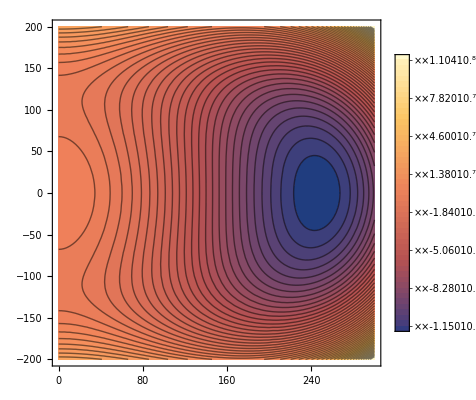

```mathematica
ContourPlot[V0[h,s],{h,0,300},{s,-200,200},PlotLegends->Automatic,Contours->50,PlotRange->{Full,Full}]
```

```mathematica
V0[246,0]
```

-1.18786×10^8

## Explicit Z_2 symmetry

## Define the Fields

```mathematica
(*Gauge Fields*)
sigpauli1={{0,1},{1,0}};
sigpauli2={{0,-ⅈ},{ⅈ,0}};
sigpauli3={{1,0},{0,-1}};
eins={{1,0},{0,1}};
(*Gauge Fields*)
gaugefields={Subscript[W, 1],Subscript[W, 2],Subscript[W, 3],B};
cw=g/Sqrt[g^2+Subscript[g, w]^2];
sw=Subscript[g, w]/Sqrt[g^2+Subscript[g, w]^2];
Rot={{cw,-sw},{sw,cw}};
(*Quark weyl spinors*)
QLbar={Subscript[t̄, L],Subscript[b̄, L]};
QL={Subscript[t, L],Subscript[b, L]};
barfermfields={Subscript[t̄, L],Subscript[t̄, R],Subscript[b̄, L],Subscript[b̄, R]};
fermfields={Subscript[t, L],Subscript[t, R],Subscript[b, L],Subscript[b, R]};
Conjugate[Subscript[y, t]]^=Subscript[y, t];
Conjugate[Subscript[y, b]]^=Subscript[y, b];
(*Scalars*)
Phi={{1/Sqrt[2] (SuperPlus[G]+ⅈ*SuperMinus[G])},{1/Sqrt[2] (Subscript[φ, H]+h+ⅈ*χ)}};
Si = Subscript[φ, S] + s;
PhiHC=Conjugate[Transpose[Phi]];
Phiwig=(I sigpauli2.Conjugate[Phi]);
PhiwigHC=ConjugateTranspose[Phiwig];
sfields={SuperPlus[G],SuperMinus[G],χ,h,s};
Conjugate[SuperPlus[G]]^=SuperPlus[G];
Conjugate[SuperMinus[G]]^=SuperMinus[G];
Conjugate[χ]^=χ;
Conjugate[h]^=h;
Conjugate[Subscript[φ, H]] ^= Subscript[φ, H];
Conjugate[s] ^= s;
UG ={SuperPlus[G]->0,SuperMinus[G]->0,χ->0,h->0,s->0};
VEV = {Subscript[φ, H]->v,Subscript[φ, S]->0};
```

## Tree-Level Potential

### Scalar Potential

```mathematica
V = Expand[-Subscript[μ, H]^2 PhiHC . Phi + 
     Subscript[λ, H] (PhiHC . Phi)^2 - 
     1/2*Subscript[μ, S]^2*Si^2 + 
     1/4*Subscript[λ, S]*Si^4 + 
     1/2*Subscript[λ, HS]*PhiHC . Phi*Si^2][[1, 1]];

V0=V/.UG
```

-1/2 μ_H^2 φ_H^2+1/4 λ_H φ_H^4-1/2 μ_S^2 φ_S^2+1/4 λ_HS φ_H^2 φ_S^2+1/4 λ_S φ_S^4

### Vacuum Expectation Values

```mathematica
D[V0,Subscript[φ, H]]/.VEV
Solve[0==D[V0,Subscript[φ, H]]/.VEV/.Subscript[μ, H]->Sqrt[x],x]/.{x->Subscript[μ, H]^2}
```

v^3 λ_H-v μ_H^2

{{μ_H^2→v^2 λ_H}}

```mathematica
Tadpole={Subscript[μ, H]^2->v^2 Subscript[λ, H]};
```

### Field Dependent Masses

#### Scalars

```mathematica
MassMatrixScalars=Table[
D[D[V,sfields[[i]]],sfields[[j]]],{i,Length[sfields]},{j,Length[sfields]}
];
MassScalars=MassMatrixScalars/.UG//Simplify;
MassScalars/.{Subscript[φ, H]->h,Subscript[φ, S]->s}//MatrixForm
PhysicalMassScalars=MassScalars/.VEV/.Tadpole//Simplify;
PhysicalMassScalars//MatrixForm
```

(h^2 λ_H+(s^2 λ_HS)/2-μ_H^2 | 0 | 0 | 0 | 0
0 | h^2 λ_H+(s^2 λ_HS)/2-μ_H^2 | 0 | 0 | 0
0 | 0 | h^2 λ_H+(s^2 λ_HS)/2-μ_H^2 | 0 | 0
0 | 0 | 0 | 3 h^2 λ_H+(s^2 λ_HS)/2-μ_H^2 | h s λ_HS
0 | 0 | 0 | h s λ_HS | (h^2 λ_HS)/2+3 s^2 λ_S-μ_S^2)

(0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 2 v^2 λ_H | 0
0 | 0 | 0 | 0 | (v^2 λ_HS)/2-μ_S^2)

```mathematica
PhysicalMassScalars[[4;;5,4;;5]]//MatrixForm
```

(2 v^2 λ_H | 0
0 | (v^2 λ_HS)/2-μ_S^2)

```mathematica
(*This Must be greater than 0 to be a minimum*)
Det[PhysicalMassScalars[[4;;5,4;;5]]]//FullSimplify
```

v^2 λ_H (v^2 λ_HS-2 μ_S^2)

```mathematica
mG2[h_,s_]:=h^2 Subscript[λ, H]+(s^2 Subscript[λ, HS])/2-Subscript[μ, H]^2
mh2[h_,s_]:=3 h^2 Subscript[λ, H]+(s^2 Subscript[λ, HS])/2-Subscript[μ, H]^2
ms2[h_,s_]:=(h^2 Subscript[λ, HS])/2+3 s^2 Subscript[λ, S]-Subscript[μ, S]^2
```

#### Fermions

```mathematica
(*Yukawa Lagrangian*)
Yuk1=Expand[-(Subscript[y, t] QLbar.Phiwig Subscript[t, R]+Subscript[y, b] QLbar.Phi Subscript[b, R])[[1]]];
Yuk2=Expand[-(Subscript[y, t] PhiwigHC.QL Subscript[t̄, R]+Subscript[y, b] PhiHC.QL Subscript[b̄, R])[[1]]];
Yuk=Yuk1+Yuk2;
Yuk/.UG/.VEV
(*Mass Matrix in Chyral Basis*)
MassFermMatrix=Table[Coefficient[Coefficient[-(Yuk1+Yuk2),barfermfields[[i]]],fermfields[[j]]],{i,4},{j,4}];
MatrixForm[MassFermMatrix/.UG/.VEV]
```

-(v b_R y_b (b̄)_L)/(√2)-(v b_L y_b (b̄)_R)/(√2)-(v t_R y_t (t̄)_L)/(√2)-(v t_L y_t (t̄)_R)/(√2)

(0 | (v y_t)/(√2) | 0 | 0
(v y_t)/(√2) | 0 | 0 | 0
0 | 0 | 0 | (v y_b)/(√2)
0 | 0 | (v y_b)/(√2) | 0)

```mathematica
mt2[v_,u_]:=((v Subscript[y, t])/(√2))^2
mb2[v_,u_]:=((v Subscript[y, b])/(√2))^2
```

#### Gauge Bosons

```mathematica
(*Gauge Mass Part of Kinetic Part*)
P=(ⅈ g (Subscript[W, 1] sigpauli1/2+Subscript[W, 2] sigpauli2/2+Subscript[W, 3] sigpauli3/2)+(ⅈ Subscript[g, w]/2) B eins).Phi[[1;;2,1]];
LGauge=Expand[ComplexExpand[Conjugate[P].P]];
LGauge/.UG/.VEV;
(*Mass Matrix in Interaction Basis*)
MassGaugeMatrix=Table[If[i==j,2 Simplify[Coefficient[LGauge,gaugefields[[i]],2]],Simplify[Coefficient[Coefficient[LGauge,gaugefields[[i]]],gaugefields[[j]]]]],{i,4},{j,4}];

MassGaugeMatrix/.UG/.VEV//MatrixForm

(*Masses of Physical Gauge Bosons*)
MG=MassGaugeMatrix/.UG/.VEV;
NeutralBlock=MG[[3;;4,3;;4]];
NeutralPhys=Simplify[Rot.NeutralBlock.Transpose[Rot]]//MatrixForm
```

((g^2 v^2)/4 | 0 | 0 | 0
0 | (g^2 v^2)/4 | 0 | 0
0 | 0 | (g^2 v^2)/4 | -1/4 g v^2 g_w
0 | 0 | -1/4 g v^2 g_w | 1/4 v^2 g_w^2)

(1/4 v^2 (g^2+g_w^2) | 0
0 | 0)

```mathematica
mW2[v_,u_]:=(g^2 v^2)/4
mZ2[v_,u_]:=1/4 v^2 (g^2+Subscript[g, w]^2)
```

## Physical Parametrization

```mathematica
D[V0,{Subscript[φ, H],2}]/.VEV/.Tadpole//Simplify
```

2 v^2 λ_H

```mathematica
D[V0,{Subscript[φ, S],2}]/.VEV/.Tadpole//Simplify
```

(v^2 λ_HS)/2-μ_S^2

```mathematica
D[V0,Subscript[φ, H],Subscript[φ, S]]/.VEV/.Tadpole//Simplify
```

0

```mathematica
Solve[2 v^2 Subscript[λ, H]==Subscript[m, H]^2&&(v^2 Subscript[λ, HS])/2-x==Subscript[m, S]^2,{Subscript[λ, H],x}]/.{x->Subscript[μ, S]^2}
```

{{λ_H→m_H^2/(2 v^2),μ_S^2→1/2 (-2 m_S^2+v^2 λ_HS)}}

```mathematica
Rotation={Subscript[λ, H]->Subscript[m, H]^2/(2 v^2),Subscript[μ, S]^2->1/2 (-2 Subscript[m, H]^2+v^2 Subscript[λ, HS])};
```

```mathematica
RotTadpole=Tadpole/.Rotation//Simplify
```

{μ_H^2→m_H^2/2}

## Thermal Masses

```mathematica
(*── Debye matrix ──*)Do[cSca[X,Y]=T^2/24*Sum[D[D[D[D[V,sfields[[X]]],sfields[[Y]]],sfields[[i]]],sfields[[i]]],{i,Length[sfields]}];
cFer[X,Y]=T^2/24*(Sum[Sum[Conjugate[D[D[D[Yuk,fermfields[[i]]],barfermfields[[j]]],sfields[[X]]]]*D[D[D[Yuk,fermfields[[i]]],barfermfields[[j]]],sfields[[Y]]],{i,Length[fermfields]}],{j,Length[barfermfields]}]+Sum[Sum[D[D[D[Yuk,fermfields[[i]]],barfermfields[[j]]],sfields[[X]]]*Conjugate[D[D[D[Yuk,fermfields[[i]]],barfermfields[[j]]],sfields[[Y]]]],{i,Length[fermfields]}],{j,Length[barfermfields]}])/. {Subscript[y, b]^2->3 Subscript[y, b]^2,Subscript[y, t]^2->3 Subscript[y, t]^2};
cGag[X,Y]=3 T^2/24*Sum[D[D[D[D[LGauge,gaugefields[[i]]],gaugefields[[i]]],sfields[[X]]],sfields[[Y]]],{i,Length[gaugefields]}];
c[X,Y]=Simplify[cSca[X,Y]+cFer[X,Y]+cGag[X,Y]];,{X,Length[sfields]},{Y,Length[sfields]}];

(*── Display ──*)ScaDeb=Table[c[a,r],{a,Length[sfields]},{r,Length[sfields]}];
ScaDeb//MatrixForm
```

(1/48 T^2 (9 g^2+3 g_w^2+12 y_b^2+12 y_t^2+24 λ_H+2 λ_HS) | 0 | 0 | 0 | 0
0 | 1/48 T^2 (9 g^2+3 g_w^2+12 y_b^2+12 y_t^2+24 λ_H+2 λ_HS) | 0 | 0 | 0
0 | 0 | 1/48 T^2 (9 g^2+3 g_w^2+12 y_b^2+12 y_t^2+24 λ_H+2 λ_HS) | 0 | 0
0 | 0 | 0 | 1/48 T^2 (9 g^2+3 g_w^2+12 y_b^2+12 y_t^2+24 λ_H+2 λ_HS) | 0
0 | 0 | 0 | 0 | 1/12 T^2 (2 λ_HS+3 λ_S))

```mathematica
Do[cV[X]=Collect[T^2 (2/3)((4/8)+5)(1/4)Sum[D[D[D[D[LGauge,gaugefields[[X]]],gaugefields[[X]]],sfields[[i]]],sfields[[i]]],{i,Length[sfields]}],T,Simplify];
,{X,Length[gaugefields]}];
VecDeb=Table[KroneckerDelta[X,Y]cV[X],{X,Length[gaugefields]},{Y,Length[gaugefields]}];
VecDeb//MatrixForm

(*Extract the 2×2 neutral block:W3=index 3,B=index 4*)
NeutralBlock=VecDeb[[3;;4,3;;4]];
(*Rotate to physical basis*)
NeutralPhys=Simplify[Rot.NeutralBlock.Transpose[Rot]];
NeutralPhys//MatrixForm
```

((11 g^2 T^2)/6 | 0 | 0 | 0
0 | (11 g^2 T^2)/6 | 0 | 0
0 | 0 | (11 g^2 T^2)/6 | 0
0 | 0 | 0 | 11/6 T^2 g_w^2)

((11 T^2 (g^4+g_w^4))/(6 (g^2+g_w^2)) | (11 g T^2 g_w (g^2-g_w^2))/(6 (g^2+g_w^2))
(11 g T^2 g_w (g^2-g_w^2))/(6 (g^2+g_w^2)) | (11 g^2 T^2 g_w^2)/(3 (g^2+g_w^2)))

## Stability Constraints

```mathematica
Solve[D[V0,Subscript[φ, H]]==0&&D[V0,Subscript[φ, S]]==0,{Subscript[φ, H],Subscript[φ, S]}]
```

{{φ_H→0,φ_S→0},{φ_H→0,φ_S→-μ_S/(√λ_S)},{φ_H→0,φ_S→μ_S/(√λ_S)},{φ_H→-(√2 √(-2 λ_S μ_H^2+λ_HS μ_S^2))/(√(λ_HS^2-4 λ_H λ_S)),φ_S→-(√2 √(λ_HS μ_H^2-2 λ_H μ_S^2))/(√(λ_HS^2-4 λ_H λ_S))},{φ_H→-(√2 √(-2 λ_S μ_H^2+λ_HS μ_S^2))/(√(λ_HS^2-4 λ_H λ_S)),φ_S→(√2 √(λ_HS μ_H^2-2 λ_H μ_S^2))/(√(λ_HS^2-4 λ_H λ_S))},{φ_H→(√2 √(-2 λ_S μ_H^2+λ_HS μ_S^2))/(√(λ_HS^2-4 λ_H λ_S)),φ_S→-(√2 √(λ_HS μ_H^2-2 λ_H μ_S^2))/(√(λ_HS^2-4 λ_H λ_S))},{φ_H→(√2 √(-2 λ_S μ_H^2+λ_HS μ_S^2))/(√(λ_HS^2-4 λ_H λ_S)),φ_S→(√2 √(λ_HS μ_H^2-2 λ_H μ_S^2))/(√(λ_HS^2-4 λ_H λ_S))},{φ_H→-μ_H/(√λ_H),φ_S→0},{φ_H→μ_H/(√λ_H),φ_S→0}}

```mathematica
(*EW Vaccum*)
V0/.{Subscript[φ, H]->Subscript[μ, H]/(√Subscript[λ, H]),Subscript[φ, S]->0}
```

-μ_H^4/(4 λ_H)

```mathematica
(*Symmetric Vacuum*)
V0/.{Subscript[φ, H]->0,Subscript[φ, S]->Subscript[μ, S]/(√Subscript[λ, S])}
```

-μ_S^4/(4 λ_S)

```mathematica
(*Asymmetric Vacuum*)
V0/.{Subscript[φ, H]->(√2 √(-2 Subscript[λ, S] Subscript[μ, H]^2+Subscript[λ, HS] Subscript[μ, S]^2))/(√(Subscript[λ, HS]^2-4 Subscript[λ, H] Subscript[λ, S])),Subscript[φ, S]->(√2 √(Subscript[λ, HS] Subscript[μ, H]^2-2 Subscript[λ, H] Subscript[μ, S]^2))/(√(Subscript[λ, HS]^2-4 Subscript[λ, H] Subscript[λ, S]))}//Simplify
```

(λ_S μ_H^4-λ_HS μ_H^2 μ_S^2+λ_H μ_S^4)/(λ_HS^2-4 λ_H λ_S)

```mathematica
(*Deeper that Symetric*)
Solve[-Subscript[μ, H]^4/(4 Subscript[λ, H])==-Subscript[μ, S]^4/(4 Subscript[λ, S]),Subscript[λ, S]]
```

{{λ_S→(λ_H μ_S^4)/μ_H^4}}

```mathematica
(*Physical Parameters*)
(Subscript[λ, H] Subscript[μ, S]^4)/Subscript[μ, H]^4/.{Subscript[λ, H]->Subscript[m, H]^2/(2 v^2),Subscript[μ, S]->Sqrt[1/2 (-2 Subscript[m, S]^2+v^2 Subscript[λ, HS])],Subscript[μ, H]->Sqrt[Subscript[m, H]^2/2]}
```

((-2 m_S^2+v^2 λ_HS)^2)/(2 v^2 m_H^2)

## High Temperature Limit

```mathematica
V0
```

-1/2 μ_H^2 φ_H^2+1/4 λ_H φ_H^4-1/2 μ_S^2 φ_S^2+1/4 λ_HS φ_H^2 φ_S^2+1/4 λ_S φ_S^4

```mathematica
Collect[V0+T^2/24*(mh2[Subscript[φ, H],Subscript[φ, S]]+ms2[Subscript[φ, H],Subscript[φ, S]]+3*mG2[Subscript[φ, H],Subscript[φ, S]]+6*mW2[Subscript[φ, H],Subscript[φ, S]]+3*mZ2[Subscript[φ, H],Subscript[φ, S]])+T^2/48*(12*mt2[Subscript[φ, H],Subscript[φ, S]]+12*mb2[Subscript[φ, H],Subscript[φ, S]])-T/(12*π)*(mh2[Subscript[φ, H],Subscript[φ, S]]^(3/2)+ms2[Subscript[φ, H],Subscript[φ, S]]^(3/2)+3*mG2[Subscript[φ, H],Subscript[φ, S]]^(3/2)+6*mW2[Subscript[φ, H],Subscript[φ, S]]^(3/2)+3*mZ2[Subscript[φ, H],Subscript[φ, S]]^(3/2)),{Subscript[φ, H],Subscript[φ, S]}]
```

-1/6 T^2 μ_H^2-1/24 T^2 μ_S^2+1/4 λ_H φ_H^4-(T (g^2 φ_H^2)^(3/2))/(16 π)-(T ((g^2+g_w^2) φ_H^2)^(3/2))/(32 π)+((T^2 λ_HS)/12+(T^2 λ_S)/8-μ_S^2/2) φ_S^2+1/4 λ_S φ_S^4+φ_H^2 ((3 g^2 T^2)/32+1/32 T^2 g_w^2+1/8 T^2 y_b^2+1/8 T^2 y_t^2+(T^2 λ_H)/4+(T^2 λ_HS)/48-μ_H^2/2+1/4 λ_HS φ_S^2)-(T (-μ_H^2+λ_H φ_H^2+1/2 λ_HS φ_S^2)^(3/2))/(4 π)-(T (-μ_H^2+3 λ_H φ_H^2+1/2 λ_HS φ_S^2)^(3/2))/(12 π)-(T (-μ_S^2+1/2 λ_HS φ_H^2+3 λ_S φ_S^2)^(3/2))/(12 π)

```mathematica
VTP[h_,s_,T_]:=-((g^2 h^2)^(3/2) T)/(16 π)-(T (h^2 (g^2+Subscript[g, w]^2))^(3/2))/(32 π)+(h^4 Subscript[λ, H])/4+(s^4 Subscript[λ, S])/4+h^2 ((3 g^2 T^2)/32+1/32 T^2 Subscript[g, w]^2+1/8 T^2 Subscript[y, b]^2+1/8 T^2 Subscript[y, t]^2+(T^2 Subscript[λ, H])/4+(s^2 Subscript[λ, HS])/4+(T^2 Subscript[λ, HS])/48-Subscript[μ, H]^2/2)+s^2 ((T^2 Subscript[λ, HS])/12+(T^2 Subscript[λ, S])/8-Subscript[μ, S]^2/2)
VTP[h,s,0]
```

(h^4 λ_H)/4+(s^4 λ_S)/4+h^2 ((s^2 λ_HS)/4-μ_H^2/2)-1/2 s^2 μ_S^2

```mathematica
VT[h_,s_,T_]:=h^2/2*(Subscript[c, H]*T^2-Subscript[μ, H]^2)+s^2/2*(Subscript[c, S]*T^2-Subscript[μ, S]^2)+h^4/4*Subscript[λ, H]+s^4/4*Subscript[λ, S]+(h^2s^2)/4*Subscript[λ, HS]-B*T*h^3
VT[h,s,T]
```

-B h^3 T+(h^4 λ_H)/4+1/4 h^2 s^2 λ_HS+(s^4 λ_S)/4+1/2 h^2 (T^2 c_H-μ_H^2)+1/2 s^2 (T^2 c_S-μ_S^2)

### EW Vacuum

```mathematica
D[VT[h,s,T],h]/.{h->v,s->0}
Solve[0==D[VT[h,s,T],h]/.{h->v,s->0},v]
```

-3 B T v^2+v^3 λ_H+v (T^2 c_H-μ_H^2)

{{v→0},{v→-(-3 B T+√(9 B^2 T^2-4 T^2 c_H λ_H+4 λ_H μ_H^2))/(2 λ_H)},{v→(3 B T+√(9 B^2 T^2-4 T^2 c_H λ_H+4 λ_H μ_H^2))/(2 λ_H)}}

```mathematica
v[T_]:=(3 B T+√(9 B^2 T^2-4 T^2 Subscript[c, H] Subscript[λ, H]+4 Subscript[λ, H] Subscript[μ, H]^2))/(2 Subscript[λ, H])
```

### Symmetric Vacuum

```mathematica
D[VT[h,s,T],s]/.{h->0,s->w}
Solve[0==D[VT[h,s,T],s]/.{h->0,s->w},w]
```

w^3 λ_S+w (T^2 c_S-μ_S^2)

{{w→0},{w→-(√(-T^2 c_S+μ_S^2))/(√λ_S)},{w→(√(-T^2 c_S+μ_S^2))/(√λ_S)}}

```mathematica
w[T_]:=(√(-T^2 Subscript[c, S]+Subscript[μ, S]^2))/(√Subscript[λ, S])
```

```mathematica
-T^2 Subscript[c, S]+Subscript[μ, S]^2/.{Subscript[c, S]->Subscript[λ, S]/4+Subscript[λ, HS]/6}
```

```mathematica
-T^2 (Subscript[λ, HS]/6+Subscript[λ, S]/4)+Subscript[μ, S]^2/.Subscript[μ, S]^2->1/2 (-2 Subscript[m, S]^2+v^2 Subscript[λ, HS])//Simplify
```

```mathematica
-Subscript[m, S]^2-1/6 (T^2-3 v^2) Subscript[λ, HS]-(T^2 Subscript[λ, S])/4
```

```mathematica
(-(T^2 Subscript[λ, S])/4-Subscript[m, S]^2)/(1/6 (T^2-3 v^2) )//Simplify
```

-(3 (4 m_S^2+T^2 λ_S))/(2 (T^2-3 v^2))

```mathematica
Solve[-Subscript[m, S]^2-1/6 (T^2-3 v^2) Subscript[λ, HS]-(T^2 Subscript[λ, S])/4==0,Subscript[λ, HS]]/.T->0
```

{{λ_HS→(2 m_S^2)/v^2}}

### Critical Temperature

```mathematica
VT[0,(√(-T^2 Subscript[c, S]+Subscript[μ, S]^2))/(√Subscript[λ, S]),T]//Simplify
```

-((-T^2 c_S+μ_S^2)^2)/(4 λ_S)

```mathematica
VT[v,0,T]
```

-B T v^3+(v^4 λ_H)/4+1/2 v^2 (T^2 c_H-μ_H^2)

```mathematica
-B T v^3+(v^4 Subscript[λ, H])/4+1/2 v^2 (3 B T v-v^2 Subscript[λ, H])//Simplify
```

-1/4 v^3 (-2 B T+v λ_H)

```mathematica
1/(32*π)*(2g^3+(g^2+gw^2)^(3/2))/.{g->2*Subscript[m, W]/v,gw->2*Sqrt[Subscript[m, Z]^2-Subscript[m, W]^2]/v}//Simplify
```

(2 m_W^3+v^3 (m_Z^2/v^2)^(3/2))/(4 π v^3)

```mathematica
(2 Subscript[m, W]^3+v^3 (Subscript[m, Z]^2/v^2)^(3/2))/(4 π v^3)/.{Subscript[m, W]->80.369,Subscript[m, Z]->91.188,Subscript[m, H]->125.2,v->246.22}
```

0.00957732

```mathematica
(*Small B limit B=*)
(3 B T+√(9 B^2 T^2-4 T^2 Subscript[c, H] Subscript[λ, H]+4 Subscript[λ, H] Subscript[μ, H]^2))/(2 Subscript[λ, H])/.B->0//Simplify
```

(√(-λ_H (T^2 c_H-μ_H^2)))/λ_H

```mathematica
VT[(√(-Subscript[λ, H] (T^2 Subscript[c, H]-Subscript[μ, H]^2)))/Subscript[λ, H],0,T]/.B->0//Simplify
```

-((-T^2 c_H+μ_H^2)^2)/(4 λ_H)

```mathematica
Solve[-((-T^2 Subscript[c, H]+Subscript[μ, H]^2)^2)/(4 Subscript[λ, H])==-((-T^2 Subscript[c, S]+Subscript[μ, S]^2)^2)/(4 Subscript[λ, S])/.{T->Sqrt[x]},x]/.{x->T^2}//Simplify
```

{{T^2→(-√λ_S μ_H^2+√λ_H μ_S^2)/(c_S √λ_H-c_H √λ_S)},{T^2→(√λ_S μ_H^2+√λ_H μ_S^2)/(c_S √λ_H+c_H √λ_S)}}

#### Numerical Example

```mathematica
SM={Subscript[m, W]->80.369,Subscript[m, Z]->91.188,Subscript[m, H]->125.2,v->246.22,Subscript[m, t]->172.4,Subscript[m, b]->4.183};
```

```mathematica
g=2*Subscript[m, W]/v/.SM;
gw=2*Sqrt[Subscript[m, Z]^2-Subscript[m, W]^2]/v/.SM;
Subscript[y, t]=Sqrt[2]*Subscript[m, t]/v/.SM;
Subscript[y, b]=Sqrt[2]*Subscript[m, b]/v/.SM;
```

```mathematica
Subscript[c, H]=1/48 (9 g^2+3 gw^2+12 Subscript[y, b]^2+12 Subscript[y, t]^2+24 Subscript[λ, H]+2 Subscript[λ, HS])/.{Subscript[λ, H]->0.1292801978686813,Subscript[λ, HS]->0.1,Subscript[λ, S]->0.01}
Subscript[c, S]=Subscript[λ, HS]/6+Subscript[λ, S]/4/.{Subscript[λ, H]->0.1292801978686813,Subscript[λ, HS]->0.1,Subscript[λ, S]->0.01}
```

0.401644

0.0191667

```mathematica
(*Tc*)
Sqrt[(-√Subscript[λ, S] Subscript[μ, H]^2+√Subscript[λ, H] Subscript[μ, S]^2)/(Subscript[c, S] √Subscript[λ, H]-Subscript[c, H] √Subscript[λ, S])]/.{Subscript[λ, H]->0.1292801978686813,Subscript[λ, HS]->0.1,Subscript[λ, S]->0.01,Subscript[μ, H]->Sqrt[7837.52],Subscript[μ, S]->Sqrt[531.2144200000002]}
Sqrt[(√Subscript[λ, S] Subscript[μ, H]^2+√Subscript[λ, H] Subscript[μ, S]^2)/(Subscript[c, S] √Subscript[λ, H]+Subscript[c, H] √Subscript[λ, S])]/.{Subscript[λ, H]->0.1292801978686813,Subscript[λ, HS]->0.1,Subscript[λ, S]->0.01,Subscript[μ, H]->Sqrt[7837.52],Subscript[μ, S]->Sqrt[531.2144200000002]}
```

133.472

143.926

```mathematica
(*v*)
(√(-(T^2 Subscript[c, H]-Subscript[μ, H]^2)))/Sqrt[Subscript[λ, H]]/.{Subscript[λ, H]->0.1292801978686813,Subscript[λ, HS]->0.1,Subscript[λ, S]->0.01,Subscript[μ, H]->Sqrt[7837.52],Subscript[μ, S]->Sqrt[531.2144200000002],T->133.4721221181227}
```

72.648

### 3 Step Transitions

```mathematica
VT[h,s,T]
```

-B h^3 T+(h^4 λ_H)/4+1/4 h^2 s^2 λ_HS+(s^4 λ_S)/4+1/2 h^2 (T^2 c_H-μ_H^2)+1/2 s^2 (T^2 c_S-μ_S^2)

```mathematica
Solve[D[VT[h,s,T],s]==0,s]
```

{{s→0},{s→-(√(-2 T^2 c_S-h^2 λ_HS+2 μ_S^2))/(√2 √λ_S)},{s→(√(-2 T^2 c_S-h^2 λ_HS+2 μ_S^2))/(√2 √λ_S)}}

```mathematica
(*Intersection*)
Solve[0==(√(-2 T^2 Subscript[c, S]-h^2 Subscript[λ, HS]+2 Subscript[μ, S]^2))/(√2 √Subscript[λ, S]),h]
```

{{h→-(√2 √(-T^2 c_S+μ_S^2))/(√λ_HS)},{h→(√2 √(-T^2 c_S+μ_S^2))/(√λ_HS)}}

```mathematica
VT[h,0,T]
```

-B h^3 T+(h^4 λ_H)/4+1/2 h^2 (T^2 c_H-μ_H^2)

```mathematica
Collect[VT[h,(√(-2 T^2 Subscript[c, S]-h^2 Subscript[λ, HS]+2 Subscript[μ, S]^2))/(√2 √Subscript[λ, S]),T],h]
```

-B h^3 T+h^4 (λ_H/4-λ_HS^2/(16 λ_S))+(T^4 c_S^2)/(4 λ_S)-(T^2 c_S μ_S^2)/(2 λ_S)+μ_S^4/(4 λ_S)-(T^2 c_S (T^2 c_S-μ_S^2))/(2 λ_S)+(μ_S^2 (T^2 c_S-μ_S^2))/(2 λ_S)+h^2 (1/2 (T^2 c_H-μ_H^2)-(λ_HS (T^2 c_S-μ_S^2))/(4 λ_S))

```mathematica
(T^4 Subscript[c, S]^2)/(4 Subscript[λ, S])-(T^2 Subscript[c, S] Subscript[μ, S]^2)/(2 Subscript[λ, S])+Subscript[μ, S]^4/(4 Subscript[λ, S])-(T^2 Subscript[c, S] (T^2 Subscript[c, S]-Subscript[μ, S]^2))/(2 Subscript[λ, S])+(Subscript[μ, S]^2 (T^2 Subscript[c, S]-Subscript[μ, S]^2))/(2 Subscript[λ, S])//Simplify
```

-((-T^2 c_S+μ_S^2)^2)/(4 λ_S)

```mathematica
-B h^3 T+h^4 (Subscript[λ, H]/4-Subscript[λ, HS]^2/(16 Subscript[λ, S]))+h^2 (1/2 (T^2 Subscript[c, H]-Subscript[μ, H]^2)-(Subscript[λ, HS] (T^2 Subscript[c, S]-Subscript[μ, S]^2))/(4 Subscript[λ, S]))-((-T^2 Subscript[c, S]+Subscript[μ, S]^2)^2)/(4 Subscript[λ, S])
```

-B h^3 T+h^4 (λ_H/4-λ_HS^2/(16 λ_S))-((-T^2 c_S+μ_S^2)^2)/(4 λ_S)+h^2 (1/2 (T^2 c_H-μ_H^2)-(λ_HS (T^2 c_S-μ_S^2))/(4 λ_S))

```mathematica
(*Bound From bellow*)
Solve[ (Subscript[λ, H]/4-Subscript[λ, HS]^2/(16 Subscript[λ, S]))==0,Subscript[λ, HS]]
```

{{λ_HS→-2 √λ_H √λ_S},{λ_HS→2 √λ_H √λ_S}}